```mathematica
(*****************Prepare**************************)
a = 5;
b = 8;

t2 = 10;
t1 = 7;
t0 = 4;
```

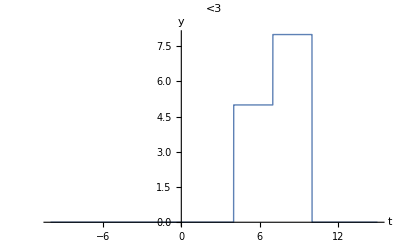

```mathematica
f2[t_] := Abs[Cos[t]];

f2[t_]:=Piecewise[{{a,t0≤t<t1},{b,t1≤t<t2},{0,True}}];
Plot[
f2[t],
{t,-10,15},
PlotStyle->Thick,
PlotLabel->"<3",
AxesLabel->{"t","y"},
PlotRange->All,
Exclusions->None
]
```

0

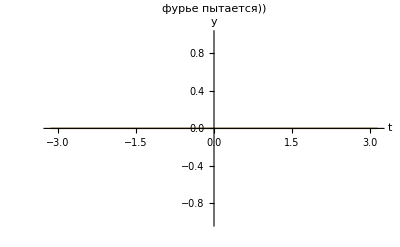

A[0] = 39/(2 π)  B[0] = 0

A[1] = -(5 Sin[2]+3 Sin[7/2]-8 Sin[5])/π  B[1] = (5 Cos[2]+3 Cos[7/2]-8 Cos[5])/π

A[2] = (-5 Sin[4]-3 Sin[7]+8 Sin[10])/(2 π)  B[2] = (5 Cos[4]+3 Cos[7]-8 Cos[10])/(2 π)

A[3] = -(5 Sin[6]+3 Sin[21/2]-8 Sin[15])/(3 π)  B[3] = (5 Cos[6]+3 Cos[21/2]-8 Cos[15])/(3 π)

A[4] = (-5 Sin[8]-3 Sin[14]+8 Sin[20])/(4 π)  B[4] = (5 Cos[8]+3 Cos[14]-8 Cos[20])/(4 π)

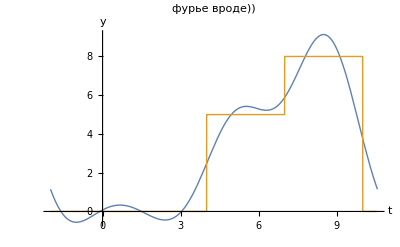

```mathematica
n =5;
h = -2;
T = 4π;

p =FourierTrigSeries[f2[t],t,n] 


Plot[
{p, f2[t]},
{t,-π,π},
PlotStyle->Thick,
PlotLabel->"фурье пытается))",
AxesLabel->{"t","y"},
PlotRange->All]



(************Попытки фора**********)
A[i_]:=(2/T) Integrate[f2[t] Cos[ (2π i)/T t],{t,h,h+T}];
B[i_] := (2/T) Integrate[f2[t] Sin[(2π i)/T t],{t,h,h+T}];
rad = 0;
For[i = 0, i≤n-1, i++,
Print["A[",i,"] = ",A[i],"  B[",i,"] = ",B[i]];
If[i == 0,
rad = rad + A[i]/2,
rad = rad + A[i] Cos[ (2π i)/T t] + B[i]Sin[(2π i)/T t]
]
]


Plot[
{rad, f2[t]},
{t,h,h + T},
PlotStyle->Thick,
PlotLabel->"фурье вроде))",
AxesLabel->{"t","y"},
PlotRange->All,
Exclusions->None
]
```